```mathematica
mz = 91.2; mw = 80.1;cw = mw/mz; sw = Sqrt[1 - cw^2];
```

```mathematica
B[g_,m_]:= g^2 sw^2 cw^2((mz^2-m^2)^3)/(2.5 6π mz^3);
```

```mathematica
B[10^-4,2]
```

0.0000283454

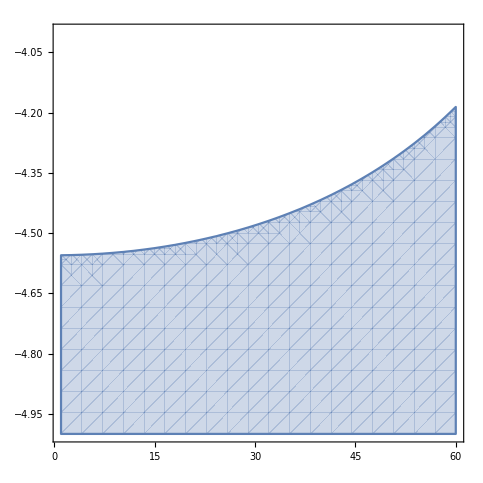

```mathematica
RegionPlot[B[10^g,m]< 2.2*10^-6, {m,1,60},{g,-5,-4} ]
```

```mathematica
mz=91.2;
 cw = 80.1/mz;
```

```mathematica
G[m_,g_]:=g^2 m^3 cw^4/(64π);
En[m_]:= mz - ((mz^2 - m^2)/(2*mz));
```

```mathematica
En[50]
```

59.3061

```mathematica
r[m_]:=En[m]/m;
```

```mathematica
l[m_,g_]:= 1.98*10^-14 r[m]/G[m,g]
```

```mathematica
l[10,10^-6]
```

0.0308745

```mathematica
1/1.98
```

0.505051

```mathematica
Solve[l[x,10^-5]== 180,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-0.360816},{x→0.-0.360813 ⅈ},{x→0.+0.360813 ⅈ},{x→0.360816}}

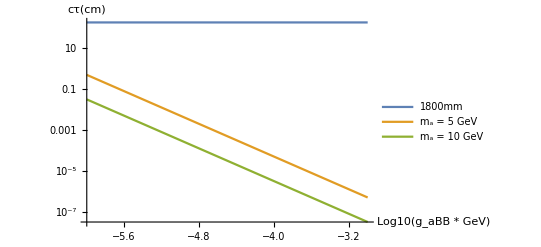

```mathematica
LogPlot[{180,l[5,10^g],l[10,10^g]},{g, -6,-3},AxesLabel->{Style["Log10(g_aBB * GeV)", Black,FontSize-> 25],Style["cτ(cm)", Black,FontSize-> 25]},PlotLegends->{Style["1800mm", 25],Style["m_a = 5 GeV",25],Style["m_a = 10 GeV",25]}, TicksStyle->Directive[Black, 20]]
```

```mathematica
?LegendMarkerSize
```

```mathematica
gaFF = g'/4 aFF
```

```mathematica
g = g'/4
```

```mathematica
g < 10^-4
```